# Pattern phase diagram for the switch model in rot. symm. spherocylinder geometry

Params used for 2D rot. symm. simulation analysed here;
Note that the nonlinear reaction rates are scaled such that the fast-growth wild-type concentrations are 1000 um^-3.

```mathematica
params={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3,
kdD->0.0015,
kdEr->1.5,
kdEl->10^-5,
kde->1,
λ->5,
μ->20,
L->50,
he->0.5,
T->3000
};
```

## Setup

## Import of simulation data from Comsol

Import functions to load the data from Comsol simulations

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->"InitializationCell"
];
```

## Analyze pattern kymographs

### Pattern test

Classify patterns based on morphological analysis.
We distinguish pattern formation driven by a dynamical instability from a parameter set that does not lead to dynamic pattern formation by testing for homogeneity in the middle of the domain (neglecting a third of the domain on the left and right).
The reason is that the non-uniform bulk-boundary ratio at the cell poles already leads to inhomogeneity of the stationary state without any pattern-forming, dynamical instability of the stationary state (cf. Thalmeier, et al., PNAS 2015)

```mathematica
ClearAll[testPatternMorphological];
Options[testPatternMorphological] = {"TimePoints" -> 200, "BoundaryPoints" -> 1};
testPatternMorphological[kymo_, opts : OptionsPattern[]] := Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,outPoints,maxIn,minIn,
morphComp,
nHighDensClusters
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

outPoints=Floor[Length[testField[[1]]]/3];
{maxIn,minIn}={Max@#,Min@#}&@Flatten[avgTF+testField[[All,outPoints;;-outPoints]]];

If[Abs[(maxIn-minIn)/minIn] < 0.05,
{I,0},(*no pattern formation*)
psAvg=Mean[Abs[Fourier[Join[#,Reverse@#]-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
wavelength=Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
period=Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];

If[period>Min[OptionValue["TimePoints"],Length@kymo]/2,
{2I,0},(*too short time window*)

morphComp=MorphologicalComponents[Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,

Print[Colorize@MorphologicalComponents[Binarize@Image@kymo[[-Min[400,Length@kymo];;;;4,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"];;4]]]];
Print["period: ",N@period,", wavelength: ",N@wavelength];

morphComp=MorphologicalComponents[ColorNegate@Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,
{5I,relContrast},
Print["inverted SW"];
{4I,relContrast}(*inverted SWs*)
],(*TWs*)

{6I,relContrast}(*SWs*)
]
]
]
];
```

Print intermediate results along the way

```mathematica
ClearAll[testPatternMorphologicalPrint];
Options[testPatternMorphologicalPrint] = {"TimePoints" -> 200, "BoundaryPoints" -> 1};
testPatternMorphologicalPrint[kymo_, opts : OptionsPattern[]] := Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,outPoints,maxIn,minIn,
morphComp,
nHighDensClusters
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

outPoints=Floor[Length[testField[[1]]]/3];
{maxIn,minIn}={Max@#,Min@#}&@Flatten[avgTF+testField[[All,outPoints;;-outPoints]]];

If[Abs[(maxIn-minIn)/minIn] < 0.05,
{I,0},(*no pattern formation*)
psAvg=Mean[Abs[Fourier[Join[#,Reverse@#]-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
Print["Time-averaged structure factor:"];
Print[ListLinePlot[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},PlotRange->All]];
wavelength=Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
Print["Spatially averaged power spectrum:"];
Print[ListLinePlot[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},PlotRange->All]];
period=Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];

If[period>Min[OptionValue["TimePoints"],Length@kymo]/2,
{2I,0},(*too short time window*)

morphComp=MorphologicalComponents[Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;
Print[ImageReflect@ImageResize[Colorize@morphComp,{500,500}]];

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,

Print["period: ",N@period,", wavelength: ",N@wavelength];

morphComp=MorphologicalComponents[ColorNegate@Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;
Print[ImageReflect@ImageResize[Colorize@morphComp,{500,500}]];

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,
{5I,relContrast},
Print["inverted SW"];
{4I,relContrast}(*inverted SWs*)
],(*TWs*)

Print["period: ",N@period,", wavelength: ",N@wavelength];
{6I,relContrast}(*SWs*)
]
]
]
];
```

### Pattern test sweep

```mathematica
ClearAll[testSweepMorph];
Options[testSweepMorph]=Options[testPatternMorphological];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
testSweepMorph[filename_,opts:OptionsPattern[]]:=Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
valuesVariedParams=Import[filename,{"/ValuesVariedParameters"}]
},
Reap[
Do[Block[{
group=StringJoin["/",Riffle[parameterNames,StringTrim[#,"."]&/@{ToString[vps[[1]]],ToString[vps[[2]]]}]],
data,
analysis
},
data=Quiet[Total[Import[filename,{{group<>"/ud",group<>"/ude"}}]]];
If[!MatrixQ[data],Continue[]];
analysis=testPatternMorphological[data,Sequence@@(List@opts)];
If[analysis[[1]]==4I||analysis[[1]]==5I,Print[Log10@vps];];
Sow@Join[vps,{analysis}];

],{vps,valuesVariedParams}];
][[-1,1]]
];
```

```mathematica
ClearAll[testSweepMultipleFilesMorph];
Options[testSweepMultipleFilesMorph]=Options[testPatternMorphological];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
testSweepMultipleFilesMorph[filenameList_,opts:OptionsPattern[]]:=
Flatten[
Reap[Do[
Sow@testSweepMorph[filename,Sequence@@(List@opts)];,
{filename,filenameList}]][[-1,1]],
1]
```

### Plot kymographs

```mathematica
ClearAll[dataKymo];
(*valuesVariedParameters is one parameter set here*)
dataKymo[filenameList_,valuesVariedParameters_]:=Block[{
kymo
},
Reap[Do[
Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
group
},
group=StringJoin["/",Riffle[parameterNames,StringTrim[#,"."|RegularExpression["\\.0*"]]&/@{ToString@SetPrecision[#[[1]],5],ToString@SetPrecision[#[[2]],5]}&@Evaluate[valuesVariedParameters]]];

If[MemberQ[Import[filename,"Datasets"],group<>"/ud"],
Sow[Import[filename,{{group<>"/ud",group<>"/ude"}}]]];
],
{filename,filenameList}];][[-1,1,1]]
];
```

### Wavelength & period analysis

```mathematica
ClearAll[analyzeKymo];
Options[analyzeKymo]={"TimePoints"->200,"BoundaryPoints"->25,"DX"->0.5,"DT"->4};
analyzeKymo[kymo_,opts:OptionsPattern[]]:=Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,outPoints,maxIn,minIn,
dx=OptionValue["DX"],
dt=OptionValue["DT"]
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

outPoints=Floor[Length[testField[[1]]]/3];
{maxIn,minIn}={Max@#,Min@#}&@Flatten[avgTF+testField[[All,outPoints;;-outPoints]]];

If[Abs[(maxIn-minIn)/minIn] < 0.05,
I,

psAvg=Mean[Abs[Fourier[#-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
wavelength=dx Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
period=dt Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];
{
relContrast,
wavelength,
period
}
]
];
```

```mathematica
ClearAll[analysisSweep];
Options[analysisSweep]=Options[analyzeKymo];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
analysisSweep[filename_,opts:OptionsPattern[]]:=Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
valuesVariedParams=Import[filename,{"/ValuesVariedParameters"}]
},

Reap[
Do[Block[{
group=StringJoin["/",Riffle[parameterNames,StringTrim[#,"."]&/@{ToString[vps[[1]]],ToString[vps[[2]]]}]],
data,
analysis
},
data=Quiet[Total[Import[filename,{{group<>"/ud",group<>"/ude"}}]]];
If[!MatrixQ[data],Continue[]];
analysis=analyzeKymo[data,Sequence@@(List@opts)];

Sow@Join[vps,{analysis}];

],{vps,valuesVariedParams}];
][[-1,1]]
];
```

```mathematica
ClearAll[analysisSweepMultipleFiles];
Options[analysisSweepMultipleFiles]=Options[analyzeKymo];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
analysisSweepMultipleFiles[filenameList_,opts:OptionsPattern[]]:=
Flatten[
Reap[Do[
Sow@analysisSweep[filename,Sequence@@(List@opts)];,
{filename,filenameList}]][[-1,1]],
1]
```

## Import Comsol data export and save as hdf5 file

Assuming that Comsol .txt export file is named “switchModel-spherocylinder2DRotSymm-rhoDEPhasediagram.txt” and saved in the same directory as this notebook.

```mathematica
data=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoDEPhasediagram.txt","ComsolSweep1DMultiComp"];
```

```mathematica
hdf5ExportSweep1D[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoDEPhasediagram.h5",data,{}];
```

## Phase diagram analysis

```mathematica
filenames={NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoDEPhasediagram.h5"};
```

#### Morphological classification: SW blue, TW red

```mathematica
analysisMorph=testSweepMultipleFilesMorph[filenames,"TimePoints"->500,"BoundaryPoints"->1];
```

-Graphics-

period: 55.5556, wavelength: 62.5

{3.,2.6}

-Graphics-

period: 100., wavelength: 83.3333

inverted SW

{3.2,2.4}

-Graphics-

period: 166.667, wavelength: 41.6667

{3.4,2.4}

-Graphics-

period: 71.4286, wavelength: 83.3333

{3.4,2.6}

-Graphics-

period: 45.4545, wavelength: 62.5

{3.4,2.8}

-Graphics-

period: 33.3333, wavelength: 62.5

{3.4,3.}

-Graphics-

period: 125., wavelength: 62.5

{3.6,2.6}

-Graphics-

period: 62.5, wavelength: 62.5

{3.6,2.8}

-Graphics-

period: 41.6667, wavelength: 62.5

{3.6,3.}

-Graphics-

period: 29.4118, wavelength: 50.

{3.6,3.2}

-Graphics-

period: 125., wavelength: 62.5

{3.8,2.8}

-Graphics-

period: 55.5556, wavelength: 71.4286

{3.8,3.}

-Graphics-

period: 35.7143, wavelength: 55.5556

{3.8,3.2}

-Graphics-

period: 25., wavelength: 41.6667

{3.8,3.4}

-Graphics-

period: 18.5185, wavelength: 55.5556

{3.8,3.6}

-Graphics-

period: 125., wavelength: 62.5

{3.8,2.8}

-Graphics-

period: 55.5556, wavelength: 71.4286

{3.8,3.}

-Graphics-

period: 35.7143, wavelength: 55.5556

{3.8,3.2}

-Graphics-

period: 25., wavelength: 41.6667

{3.8,3.4}

-Graphics-

period: 18.5185, wavelength: 55.5556

{3.8,3.6}

-Graphics-

period: 14.2857, wavelength: 45.4545

{3.8,3.8}

-Graphics-

period: 166.667, wavelength: 31.25

{4.,3.}

-Graphics-

period: 55.5556, wavelength: 62.5

{4.,3.2}

-Graphics-

period: 31.25, wavelength: 50.

{4.,3.4}

-Graphics-

period: 21.7391, wavelength: 41.6667

{4.,3.6}

-Graphics-

period: 16.129, wavelength: 38.4615

{4.,3.8}

-Graphics-

period: 12.5, wavelength: 35.7143

{4.,4.}

-Graphics-

period: 9.43396, wavelength: 35.7143

{4.,4.2}

-Graphics-

period: 13.1579, wavelength: 45.4545

{4.,3.95424}

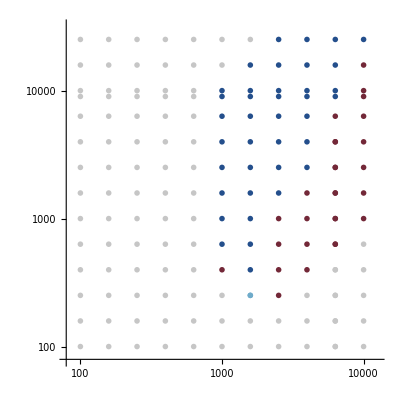

```mathematica
ListLogLogPlot[DeleteCases[{
{#[[1]],#[[2]]}&/@Select[Flatten/@analysisMorph,Im@#[[3]]<4&],(*steady state*)
{#[[1]],#[[2]]}&/@Select[Flatten/@analysisMorph,Im@#[[3]]==5&],(*TW*)
{#[[1]],#[[2]]}&/@Select[Flatten/@analysisMorph,(Im@#[[3]]==6)&],(*SW*){#[[1]],#[[2]]}&/@Select[Flatten/@analysisMorph,Im@#[[3]]==4&],(*inverted SW*)
{#[[1]],#[[2]]}&/@Select[Flatten/@analysisMorph,Im@#[[3]]==2&](*too short time window*)
},{}],
PlotMarkers->({Graphics[{#,Disk[]}],0.03}&/@{Lighter@Lighter@Gray,
ColorData["RedBlueTones"][0],ColorData["RedBlueTones"][1],ColorData["RedBlueTones"][0.8],Gray}),
PlotRange->{{10^1.9,10^4.1},{10^1.9,10^4.5}},
AspectRatio->1
]
```

## Illustration of classification scheme

## SW

```mathematica
data=dataKymo[filenames,{10^3,10^3.}];
```

```mathematica
ListDensityPlot[Total@data[[{1,2},-500;;]],InterpolationOrder->0,AspectRatio->1,PlotLegends->Automatic,ColorFunction->GrayLevel]
```

```mathematica
ListDensityPlot[Total@data[[{1,2},-500;;]],InterpolationOrder->0,AspectRatio->1,Frame->None,ColorFunction->GrayLevel]
```

```mathematica
testPatternMorphologicalPrint[Total[data],"TimePoints"->500,"BoundaryPoints"->1]
```

## TW

```mathematica
data=dataKymo[filenames,{10^3.8,10^3}];
```

```mathematica
ListDensityPlot[Total@data[[{1,2},-500;;]],InterpolationOrder->0,AspectRatio->1,PlotLegends->Automatic,ColorFunction->GrayLevel]
```

```mathematica
ListDensityPlot[Total@data[[{1,2},-500;;]],InterpolationOrder->0,AspectRatio->1,Frame->None,ColorFunction->GrayLevel]
```

```mathematica
testPatternMorphologicalPrint[Total[data],"TimePoints"->500,"BoundaryPoints"->1]
```

## (inverted) SW

```mathematica
data=dataKymo[filenames,{10^3.2,10^2.4}];
```

```mathematica
ListDensityPlot[Total@data[[{1,2},-500;;]],InterpolationOrder->0,AspectRatio->1,PlotLegends->Automatic,ColorFunction->GrayLevel]
```

```mathematica
ListDensityPlot[Total@data[[{1,2},-500;;]],InterpolationOrder->0,AspectRatio->1,Frame->None,ColorFunction->GrayLevel]
```

```mathematica
testPatternMorphologicalPrint[Total[data],"TimePoints"->500,"BoundaryPoints"->1]
```

## Patterns close at high-rhoD onset of pattern formation

```mathematica
data=dataKymo[filenames,{10^4,10^3}];
ListDensityPlot[Total@data[[{1,2},-500;;;;5]],InterpolationOrder->0,AspectRatio->1,PlotLegends->Automatic,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
data=dataKymo[filenames,{10^3.4,10^2.4}];
ListDensityPlot[Total@data[[{1,2},-500;;;;5]],InterpolationOrder->0,AspectRatio->1,PlotLegends->Automatic,ColorFunction->GrayLevel]
```

-Graphics-

## Kymographs of single data points

#### rhoD=10^3, rhoE=10^3

```mathematica
data=dataKymo[filenames,{10^3,10^3}];
```

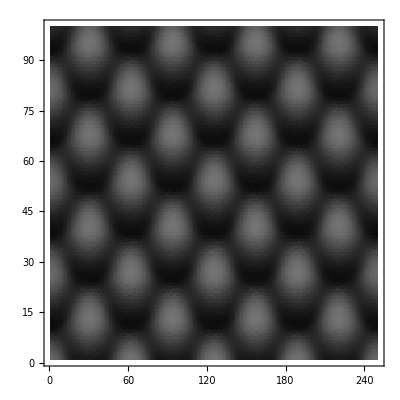

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3]&),
ColorFunctionScaling->False]
```

#### rhoD=10^3, rhoE=10^3.8

```mathematica
data=dataKymo[filenames,{10^3,10^3.8}];
```

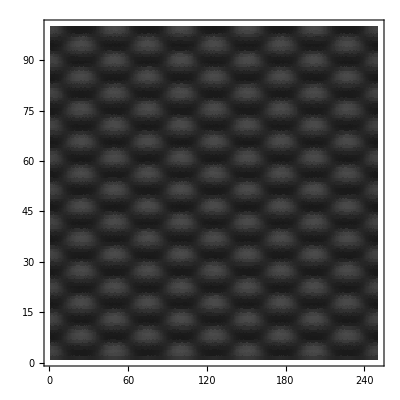

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3]&),
ColorFunctionScaling->False]
```

#### rhoD=10^3.4, rhoE=10^3

```mathematica
data=dataKymo[filenames,{10^3.4,10^3}];
```

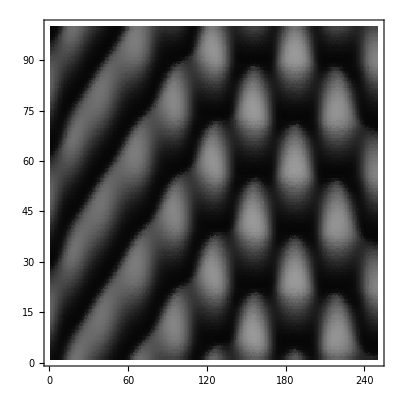

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3.4]&),
ColorFunctionScaling->False]
```

#### rhoD=10^3.8, rhoE=10^3

```mathematica
data=dataKymo[filenames,{10^3.8,10^3}];
```

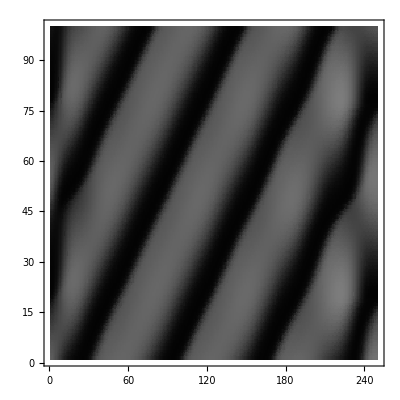

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3.8]&),
ColorFunctionScaling->False]
```

#### rhoD=10^3.8, rhoE=10^3.8

```mathematica
data=dataKymo[filenames,{10^3.8,10^3.8}];
```

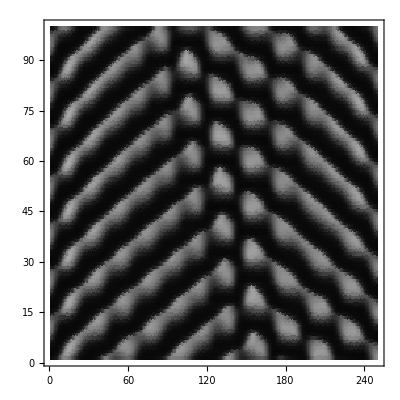

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3.8]&),
ColorFunctionScaling->False]
```

#### rhoD=10^3.6, rhoE=10^3.8

```mathematica
data=dataKymo[filenames,{10^3.6,10^3.8}];
```

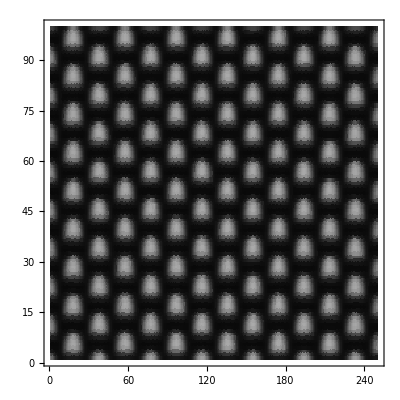

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3.6]&),
ColorFunctionScaling->False]
```

#### rhoD=10^3.8, rhoE=10^4

```mathematica
data=dataKymo[filenames,{10^3.8,10^4}];
```

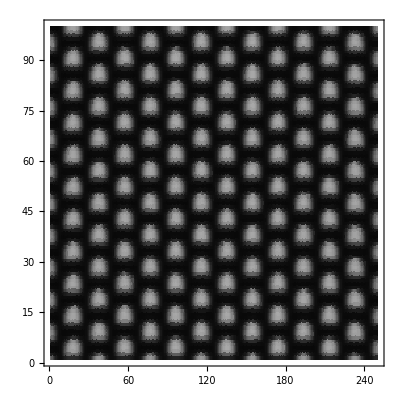

```mathematica
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,
ColorFunction->(GrayLevel[#/10^3.8]&),
ColorFunctionScaling->False]
```

## Analyze wavelength and period (not included in manuscript)

```mathematica
analysisWP=analysisSweepMultipleFiles[filenames,"TimePoints"->500,"BoundaryPoints"->1,"DX"->0.2,"DT"->2];
```

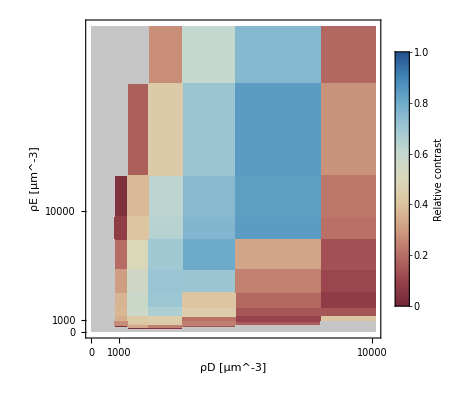

```mathematica
ListDensityPlot[Join[
{#[[1]],#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{#[[1]],#[[2]],#[[3,1]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{0,10100},{0,25200},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["Relative contrast",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{0,1000,10000},None},{{0,1000,10000},None}},
FrameTicksStyle->Directive["Label",12,Black]]
```

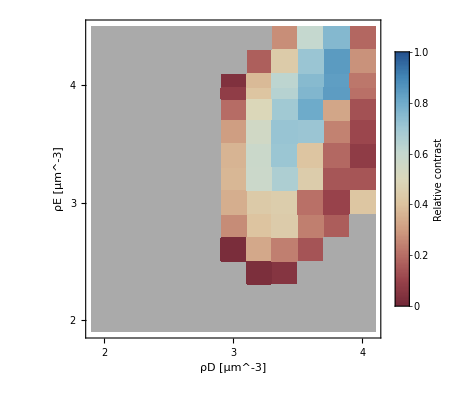

```mathematica
ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,1]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["Relative contrast",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]
```

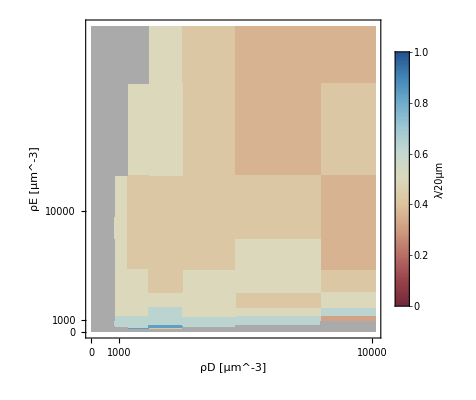

```mathematica
ListDensityPlot[Join[
{#[[1]],#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{#[[1]],#[[2]],#[[3,2]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{0,10100},{0,25200}},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["λ/20μm",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{0,1000,10000},None},{{0,1000,10000},None}},
FrameTicksStyle->Directive["Label",12,Black]]
```

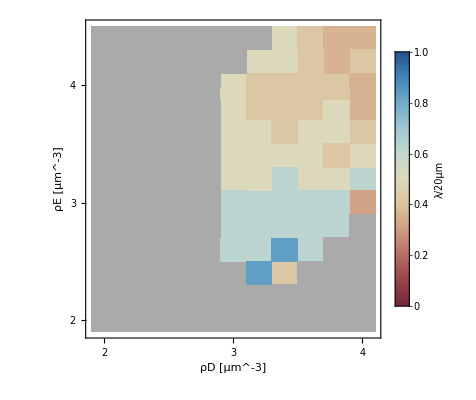

```mathematica
ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,2]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["λ/20μm",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]
```

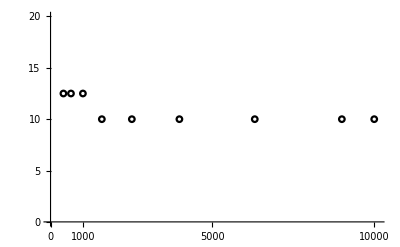

```mathematica
ListPlot[{#[[2]],#[[3,2]]}&/@Select[analysisWP,(Abs[#[[1]]-1000]<1&&ListQ@#[[3]])&],
PlotRange->{{0,10100},{0,20}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,5,10,15,20}}
]
```

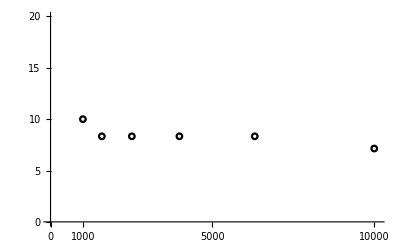

```mathematica
ListPlot[{#[[1]],#[[3,2]]}&/@Select[analysisWP,(Abs[#[[2]]-9000]<100&&ListQ@#[[3]])&],
PlotRange->{{0,10100},{0,20}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,5,10,15,20}}
]
```

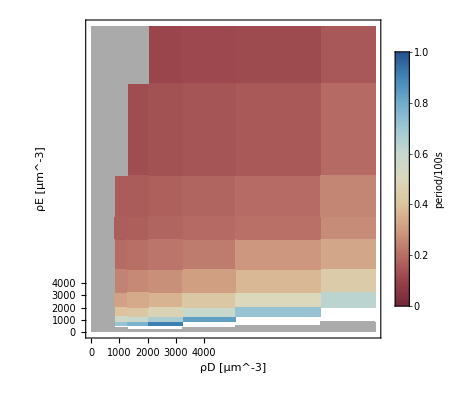

```mathematica
ListDensityPlot[Join[
{#[[1]],#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{#[[1]],#[[2]],#[[3,3]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/100],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{0,10100},{0,25200}},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["period/100s",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{0,1000,2000,3000,4000},None},{{0,1000,2000,3000,4000},None}},
FrameTicksStyle->Directive["Label",12,Black]]
```

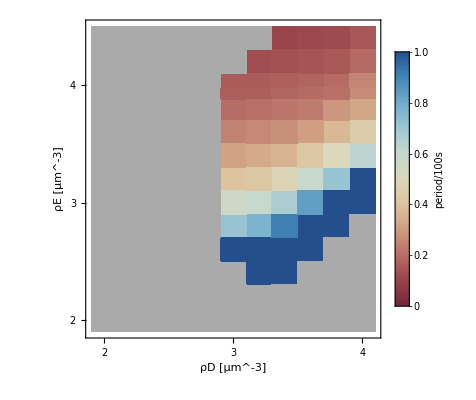

```mathematica
ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,3]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/100],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["period/100s",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]
```

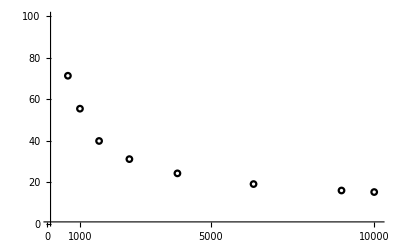

```mathematica
ListPlot[{#[[2]],#[[3,3]]}&/@Select[analysisWP,(Abs[#[[1]]-10^3]<1&&ListQ@#[[3]])&],
PlotRange->{{100,10100},{1,100}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,20,40,60,80,100}}
]
```

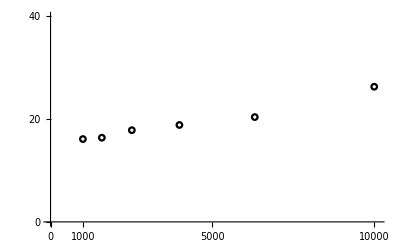

```mathematica
ListPlot[{#[[1]],#[[3,3]]}&/@Select[analysisWP,(Abs[#[[2]]-9000]<1&&ListQ@#[[3]])&],
PlotRange->{{0,10100},{0,40}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,20,40}}
]
```

```mathematica
Grid[{{ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,2]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["λ/20μm",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]
,
ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,3]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/100],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["period/100s",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]}}]
```

-Graphics- | -Graphics-

```mathematica
Export[NotebookDirectory[]<>"switchModel-2DrotSymm-periodWavelength-densityDiagram.pdf",
Grid[{{ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,2]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["λ/20μm",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]
,
ListDensityPlot[Join[
{Log10@#[[1]],Log10@#[[2]],-1}&/@Select[analysisWP,Im@#[[3]]!=0&],
{Log10@#[[1]],Log10@#[[2]],#[[3,3]]}&/@Select[analysisWP,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/100],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.1},{1.9,4.5},All},
AspectRatio->1,
PlotLegends->Placed[BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Style["period/100s",FontSize->14],LabelStyle->{Gray,FontSize->12}],Right],
FrameLabel->(Style[#,FontSize->14]&/@{"ρD [μm^-3]","ρE [μm^-3]"}),
FrameStyle->Directive[Thickness[0.003],Black],
FrameTicks->{{{2,3,4},None},{{2,3,4},None}},
FrameTicksStyle->Directive["Label",12,Black]]}}]];
```